# Cálculo de pârametros unitários de uma linha de transmissão

## Antonio Carlos S Lima EEE457 - Transmissão de Energia Elétrica 2023/2

## Início

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\anton\Dropbox\UFRJ\cursos\EEE457-Transmissão_Energia_Elétrica\arquivos_Mma_EEE457

```mathematica
<<LineCableParam2020`
```

```mathematica
dadoscond=Import["condcompleta.txt","Table"];
camp=Import["campos.txt","CSV"];
```

### Algumas constantes

```mathematica
μ= 4.0 π 10^-7;
ϵ= 8.854 10^-12;
σs=10.0^-3;
ℓ=180. 10^3; (* comprimento do circuito *)
```

cabos pararraios possuem permeabilidade magnética relativa próximo a 100

```mathematica
μr= 90.0;
```

## Circuito 230kV -- 230CST3

Dados dos condutores -- código desenvolvido pelo Prof. Robson Dias

### Dados do condutor

```mathematica
Nome=ToUpperCase["grosbeak"];
```

```mathematica
pos=Module[{posicao},posicao=If[NumberQ[Position[dadoscond,Nome][[1,1]]],Position[dadoscond,Nome][[1,1]],1];If[NumberQ[Position[dadoscond,Nome][[1,1]]],,Print["O condutor especificado não exite na tabela, verifique o nome digitado. Para não ocorrer erros nos cálculos foram utilizados os valores do condutor Owl"]];Return[posicao]];

{nome,MCM,NAl,DAl,NACO,DACO,secAl,secACO,Dcond,DALMA,PesoAl,PesoACO,Massa,CargaRupturaClasseA,CargaRupturaClasseB,Ampacidade,RMG,ResCC,ResAC,Xind,Xcap}=dadoscond[[pos]];

Table[Print[i,")  ",camp[[i,1]], " = ",dadoscond[[pos,i]]],{i,1,Length[camp]}];
```

Return[27]

1)  Nome comercial = GROSBEAK

2)  Bitola (MCM) = 636

3)  Num. de Fios de Al. = 26

4)  Diâmetro dos Fios de Al. (mm) = 3.973

5)  Num. de Fios de Aço = 7

6)  Diâmetro dos Fios de Aço (mm) = 3.089

7)  Seção transversal de Al (mm^2) = 322.33

8)  Seção transversal do cond. (mm^2) = 374.8

9)  Diâmetro do cond. (mm) = 25.16

10)  Diâmetro da Alma de Aço (mm) = 9.27

11)  Peso Nominal do Al (aprox.) (kg/km) = 893

12)  Peso nominal do Aço (aprox.) (kg/km) = 409.8

13)  Massa (aprox.) (kg/km) = 1302.8

14)  Carga de ruptura (Classe A) (kgf) = 11427

15)  Carga de ruptura (Classe B) (kgf) = 11067

16)  Ampacidade (A) = 790

17)  Raio médio geométrico (m) = 0.01021

18)  Resistência elétrica máxima CC a 20.baC (Ohm/km) = 0.09

19)  Resistência elétrica máxima CA @ 60 Hz e 75.baC (Ohm/km) = 0.108

20)  Reatância indutiva (Ohm/km) = 0.3457

21)  Reatância capacitiva (Mohm/km) = 0.2089

### Dados condutores de fase (Dove)

```mathematica
r0=(dadoscond[[pos,10]]/2)*10^-3;   (* ⟹ [m] ⟸ *)
r1=(dadoscond[[pos,9]]/2)*10^-3;

ρAl=0.028264;    (* resistividade ⟹ Ω × mm^2/ m ⟸ *)
ρAlmetro=0.028264*10^-6;    (* ⟹ Ω × m ⟸ *)

Rdc=(dadoscond[[pos,19]])*10^-3;  (* ⟹ [Ω/m] ⟸⟹ @ 20^o ⟸*)

σϕ=(1/ρAlmetro)*(dadoscond[[pos,3]]*(dadoscond[[pos,4]]*10^-3/2)^2)/(r1^2-r0^2);
```

```mathematica
svao=0.45; (* comprimento do vão em [km] *)
T=dadoscond[[pos,15]];
W=dadoscond[[pos,13]];
H=0.24*T;
Ccat=H/W;
```

```mathematica
(*flecha em metro *)
flechacond=1000*Ccat*(Cosh[svao/(2*Ccat)]-1)
```

12.4283

### Cabos guarda ou cabos pararraios (3/8 EHS)

```mathematica
Tpr=6980; (*{kgf]*)
Wpr=410; (*[kg/km]*)
Hpr=0.25*Tpr;
Ccatpr=Hpr/Wpr;
(*flecha em metro*)
flechapr=1000*Ccatpr*(Cosh[svao/(2*Ccatpr)]-1)
```

5.94873

```mathematica
npr =2;
rpr=4.57*10^-3;
Rdcpr=4.19*10^-3;
```

### Cabos guarda ou cabos pararraios (OPGW)

```mathematica
Tpr2=101.9 101.972; (*{kgf]*)
Wpr2=724; (*[kg/km]*)
Hpr2=0.25*Tpr2;
Ccatpr2=Hpr2/Wpr2;
(*flecha em metro*)
flechapr2=1000*Ccatpr2*(Cosh[svao/(2*Ccatpr2)]-1)
```

7.05701

```mathematica
rpr2=14.70/2*10^-3;
Rdcpr2= 0.511*10^-3;
```

## Visualiza Circuito

```mathematica
xc={-4.3,0, 4.3, -3.5,3.5};
yc=31 -{6.9,2.7, 6.9, .5,.5};
fl=Join[flechacond{1, 1, 1},flechapr{1,1}];
yc= yc-2/3 fl;
```

```mathematica
mostra=Table[{Circle[{xc[[i]],yc[[i]]},{0.09,0.20}]},{i,1,Length[xc]}];
o1=tsimples=Show[Graphics[mostra],Axes->False,Frame->Automatic,AspectRatio-> 1,PlotRange->{{-5,5},{5,25.}},BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,FrameLabel->{Style["Distance [m]",Bold,18],Style["Distance [m]",Bold,18]}]
```

-Graphics-

## Cálculo das matrizes

faz parte do arquivo LineCableParam2020.wl

```mathematica
Vn= 230. 10^3;
ω= 2. π 60;
ρs= 1000.;
```

```mathematica
{Zmat, Ymat} =cZYlt[ω,xc,yc,1/ρs, Rdc,r1,r0, npr, Rdcpr,rpr];
```

```mathematica
MatrixForm[Zmat 1000]
```

(0.207856+0.897094 ⅈ | 0.103243+0.413563 ⅈ | 0.0992273+0.390211 ⅈ
0.103243+0.413563 ⅈ | 0.216211+0.889551 ⅈ | 0.103243+0.413563 ⅈ
0.0992273+0.390211 ⅈ | 0.103243+0.413563 ⅈ | 0.207856+0.897094 ⅈ)

```mathematica
MatrixForm[Ymat 1000]
```

(3.×10^-9+2.91323×10^-6 ⅈ | 0.-4.7918×10^-7 ⅈ | 0.-3.19946×10^-7 ⅈ
0.-4.7918×10^-7 ⅈ | 3.×10^-9+2.98473×10^-6 ⅈ | 0.-4.7918×10^-7 ⅈ
0.-3.19946×10^-7 ⅈ | 0.-4.7918×10^-7 ⅈ | 3.×10^-9+2.91323×10^-6 ⅈ)

```mathematica
Zs =(Zmat[[1,1]]+Zmat[[2,2]]+Zmat[[3,3]])/3
```

0.210641+0.89458 ⅈ

```mathematica
Zm = Zmat[[1,2]]+ Zmat[[1,3]]+Zmat[[2,3]])/3
```

0.101904+0.405779 ⅈ

```mathematica
Zabc = Table[If[i!= j, Zm, Zs],{i,1,3},{j,1,3}];
MatrixForm[Zabc ]
```

(0.210641+0.89458 ⅈ | 0.101904+0.405779 ⅈ | 0.101904+0.405779 ⅈ
0.101904+0.405779 ⅈ | 0.210641+0.89458 ⅈ | 0.101904+0.405779 ⅈ
0.101904+0.405779 ⅈ | 0.101904+0.405779 ⅈ | 0.210641+0.89458 ⅈ)

```mathematica
Ys = (Ymat[[1,1]]+Ymat[[2,2]]+Ymat[[3,3]])/3
```

3.×10^-9+2.93707×10^-6 ⅈ

```mathematica
Ym = (Ymat[[1,2]]+ Ymat[[1,3]]+Ymat[[2,3]])/3
```

0.-4.26102×10^-7 ⅈ

```mathematica
Yabc = Table[If[i!= j, Ym, Ys],{i,1,3},{j,1,3}];
MatrixForm[Yabc ]
```

(3.×10^-9+2.93707×10^-6 ⅈ | 0.-4.26102×10^-7 ⅈ | 0.-4.26102×10^-7 ⅈ
0.-4.26102×10^-7 ⅈ | 3.×10^-9+2.93707×10^-6 ⅈ | 0.-4.26102×10^-7 ⅈ
0.-4.26102×10^-7 ⅈ | 0.-4.26102×10^-7 ⅈ | 3.×10^-9+2.93707×10^-6 ⅈ)

```mathematica
a= Exp[I 120 Degree];
A={{1,1,1},{1,a^2,a},{1,a,a^2}};
MatrixForm[A]
```

(1 | 1 | 1
1 | ⅇ^(240 ⅈ °) | ⅇ^(120 ⅈ °)
1 | ⅇ^(120 ⅈ °) | ⅇ^(240 ⅈ °))

```mathematica
Z012= Inverse[A].Zabc. A;
MatrixForm[Z012]
```

(0.41445+1.70614 ⅈ | -1.11022×10^-16-1.11022×10^-16 ⅈ | -1.11022×10^-16-1.11022×10^-16 ⅈ
-5.55112×10^-17-4.16334×10^-17 ⅈ | 0.108737+0.4888 ⅈ | 0.-3.46945×10^-17 ⅈ
-5.55112×10^-17-4.16334×10^-17 ⅈ | 0.-4.16334×10^-17 ⅈ | 0.108737+0.4888 ⅈ)

```mathematica
MatrixForm[1000Inverse[A].Zmat.A]
```

(0.41445+1.70614 ⅈ | 0.00250193-0.00620586 ⅈ | -0.0066254+0.000936193 ⅈ
-0.0066254+0.000936193 ⅈ | 0.108737+0.4888 ⅈ | -0.0157144+0.00894794 ⅈ
0.00250193-0.00620586 ⅈ | 0.0156064+0.00913514 ⅈ | 0.108737+0.4888 ⅈ)

comparando os resultados dos termos da diagonal

```mathematica
Diagonal[1000Inverse[A].Zmat.A] -Diagonal[Z012]
```

{-5.55112×10^-17+0. ⅈ,5.55112×10^-17+0. ⅈ,1.38778×10^-17+0. ⅈ}

```mathematica
Y012=   Inverse[A].Yabc. A;
MatrixForm[Y012*10^6 ]
```

(0.003+2.08486 ⅈ | 2.11758×10^-16+3.70577×10^-16 ⅈ | 2.11758×10^-16+3.70577×10^-16 ⅈ
-2.11758×10^-16+1.05879×10^-16 ⅈ | 0.003+3.36317 ⅈ | 0.-2.11758×10^-16 ⅈ
-2.11758×10^-16+1.05879×10^-16 ⅈ | 0.-2.11758×10^-16 ⅈ | 0.003+3.36317 ⅈ)

```mathematica
Z0= Z012[[1,1]]
```

0.41445+1.70614 ⅈ

```mathematica
Zpos= Z012[[2,2]]
```

0.108737+0.4888 ⅈ

```mathematica
Ypos=Y012[[2,2]]
```

0.003+3.36317 ⅈ

```mathematica
Zc= Sqrt[Zpos/Ypos]
```

0.383575-0.0419761 ⅈ

```mathematica
Pn = (Vn^2/Zc) 10^-6
```

136281.+14913.8 ⅈ

## Avaliação do desequilibrio do circuito

Matriz de rotação das fases

```mathematica
r={{0,1,0}, {0,0,1}, {1, 0,0}};
```

```mathematica
Ztrans=1/3(Inverse[r].Zmat.r + Inverse[r].Inverse[r].Zmat.r.r+Inverse[r].Inverse[r].Inverse[r].Zmat.r.r.r  );
MatrixForm[Ztrans]
```

(0.000210641+0.00089458 ⅈ | 0.000101904+0.000405779 ⅈ | 0.000101904+0.000405779 ⅈ
0.000101904+0.000405779 ⅈ | 0.000210641+0.00089458 ⅈ | 0.000101904+0.000405779 ⅈ
0.000101904+0.000405779 ⅈ | 0.000101904+0.000405779 ⅈ | 0.000210641+0.00089458 ⅈ)

```mathematica
Ytrans=1/3(Inverse[r].Ymat.r + Inverse[r].Inverse[r].Ymat.r.r+Inverse[r].Inverse[r].Inverse[r].Ymat.r.r.r  );
MatrixForm[Ytrans]
```

(3.×10^-12+2.93707×10^-9 ⅈ | 0.-4.26102×10^-10 ⅈ | 0.-4.26102×10^-10 ⅈ
0.-4.26102×10^-10 ⅈ | 3.×10^-12+2.93707×10^-9 ⅈ | 0.-4.26102×10^-10 ⅈ
0.-4.26102×10^-10 ⅈ | 0.-4.26102×10^-10 ⅈ | 3.×10^-12+2.93707×10^-9 ⅈ)

```mathematica
Aqt= IdentityMatrix[3] + (Ztrans ℓ) .( Ytrans ℓ)/2 ;
Bqt= (Ztrans ℓ) ;
Cqt= (Ytrans ℓ).(IdentityMatrix[3] + (Ztrans ℓ) .( Ytrans ℓ)/4);
```

```mathematica
Qlm=ArrayFlatten[{{Aqt, Bqt}, {Cqt, Aqt}}];
```

```mathematica
Vs=230 10^3/Sqrt[3]{1, a^2,a};
```

```mathematica
MatrixForm[Bqt]
```

(37.9154+161.024 ⅈ | 18.3428+73.0403 ⅈ | 18.3428+73.0403 ⅈ
18.3428+73.0403 ⅈ | 37.9154+161.024 ⅈ | 18.3428+73.0403 ⅈ
18.3428+73.0403 ⅈ | 18.3428+73.0403 ⅈ | 37.9154+161.024 ⅈ)

```mathematica
aux= Bqt /Re[Zc] ;
vabc=Inverse[Aqt+ aux].Vs
```

{124.818-550.603 ⅈ,-539.245+167.205 ⅈ,414.427+383.397 ⅈ}

```mathematica
Abs[vabc]
```

{564.573,564.573,564.573}

```mathematica
ang1=Table[Arg[vabc[[i]]]/π 180 ,{i,3}]
```

{-77.2273,162.773,42.7727}

```mathematica
ang2=Arg[vabc[[1]]]/π 180  +{0, -120, 120}
```

{-77.2273,-197.227,42.7727}

```mathematica
ang2-ang1
```

{0.,-358.861,3.90528}

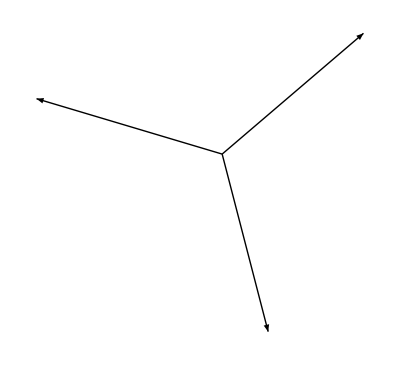

```mathematica
Graphics[Table[Arrow[{{0,0},{Re[iabc[[i]]],Im[iabc[[i]]] }}],{i,3}]]
```

### Cálculo das tensões de sequência

```mathematica
vabcL=  Re[Zc]DiagonalMatrix[{1,1,1}].iabc
```

{83.0775-321.455 ⅈ,-335.206+100.239 ⅈ,255.154+218.58 ⅈ}

```mathematica
Abs[vabcL ]
```

{332.017,349.873,335.978}

```mathematica
v012=Inverse[A].vabcL
```

{1.0086-0.87863 ⅈ,75.1967-330.711 ⅈ,6.87224+10.1342 ⅈ}

### Cálculo dos desequilibrios de tensão

```mathematica
Table[100 Abs[v012[[i]]/v012[[2]]],{i,3}]
```

{0.394405,100.,3.61036}

A tensão de sequência zero é menor que 0,3%, e de sequência negativa menor qu 1%